# Moving point heat source

In this short notice we explore solution to moving heat source given by the paper “Solutions for modelling moving heat sources in semi-infinite medium and applications to laser material processing”
by M.Van Elsen, M.Baelmans, P.Mercelis, J.-P.Kruth  doi:10.1016/j.ijheatmasstransfer.2007.02.044.

Moving point heat source in 3 D semi-inifite body is described by Carslaw and Jaeger:
k  conductivity (W/mK)
T0   room temperature (K)
Tm melting temperature (K)
V scan speed (m/s)
x coordinate along scanning direction (m)
y coordinate perpendicular to scanning direction (m)
z coordinate in depth (m)
P laser power (W)

Values of thermal parameters for Ti - 6 Al - 4 V

```mathematica
Tm=1933;
T0=293;
k=6.0;
κ =2.4 10^-6;
```

```mathematica
θ[P_,κ_,V_,x_,y_,z_]:= P/(4 π k √(x^2+y^2+z^2)(Tm-T0)) Exp[-V(√(x^2+y^2+z^2)+x)/(2 κ)];
```

Result for moving point source

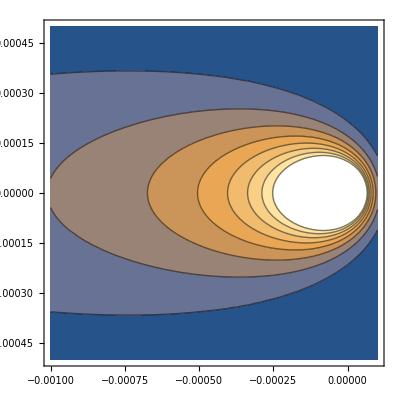

```mathematica
ContourPlot[θ[25.0,κ,0.05,x,y,0.0],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4}]
```

This are results for Uniform moving heat source:
The solution is given by M.Van Elsen et al. International Journal of Heat and mass transfer.
50 (2007) 4872-4882.

```mathematica
θunif[P_,κ_,V_,x_,y_,z_,t_]:=-1/(2^5 η)NIntegrate[
```